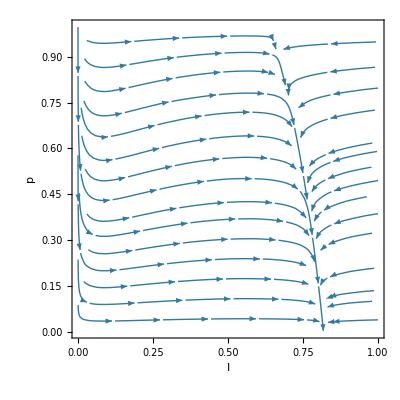

./figures/6_055_cata_disappearence.png

-Graphics-

```mathematica
(*定义参数和方程*)
ClearAll["Global`*"]
mu=1;                  (*恢复速率*)
be=0.55;                  (*传播速率与接触人数的乘积*)
alp = 0.5;              (*防护效果*)
w=1;                       (*行为更新速率*)
c0=1;                 (*采取防护措施的花费*)
cI=6;               (*被感染后的代价*)
k = 10;
gam = 1;           (*对传播参数的误判，与媒体宣传有关*)
ita = 0.001;             (*社会一致性的影响强度*)

f[x_,y_]:=-mu*x +be*k*(1-alp*y)*(1-x)*x 
g[x_,y_]:=w*y*(1-y)*(-c0+ cI*(Exp[-(1-alp)*be*k*gam*x]-Exp[-be*k*gam*x]) +2*ita*(2*y-1))
(*t = Log[r]/((1-r)*(-be))*)
(*绘制向量场*)
(*VectorPlot[{f[x,y],g[x,y]},(*向量场定义*){x,0,1},(*x 的范围*){y,0,1},(*y 的范围*)VectorScale->{Small,Automatic,None},(*箭头大小*)VectorStyle->Arrowheads[0.02],(*箭头样式*)Axes->True,(*显示坐标轴*)Frame->True                            (*显示边框*)]*)
img = StreamPlot[{f[x,y],g[x,y]},{x,0,1},{y,0,1},Frame->True,FrameLabel->{Style["I",Black, 25],Style["p",Black, 25]},StreamPoints->30,StreamScale-> 0.15,StreamStyle->Thickness,FrameTicksStyle->Directive[FontSize->25,Black],PlotRangePadding->Scaled[0.0], StreamColorFunction->None]
SetDirectory[NotebookDirectory[]];
Export["./figures/6_055_cata_disappearence.png",img,ImageResolution->400]
```

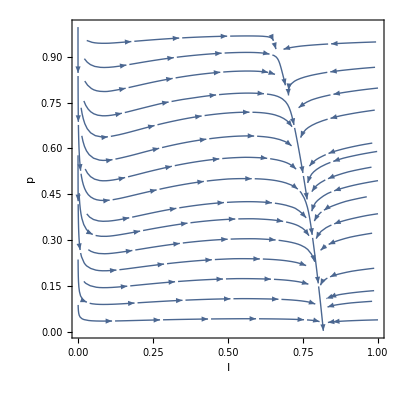

-Graphics-

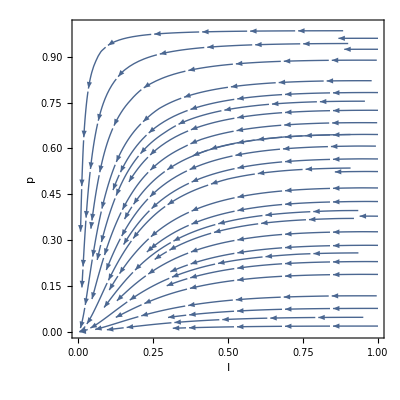

-Graphics-

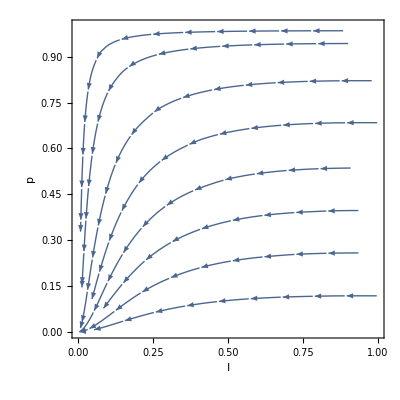

-Graphics-

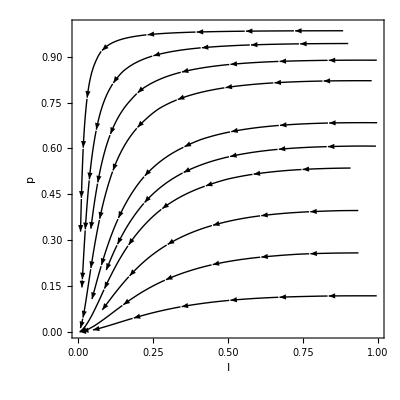

-Graphics-

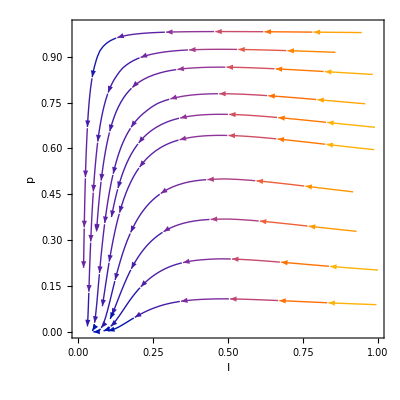

-Graphics-

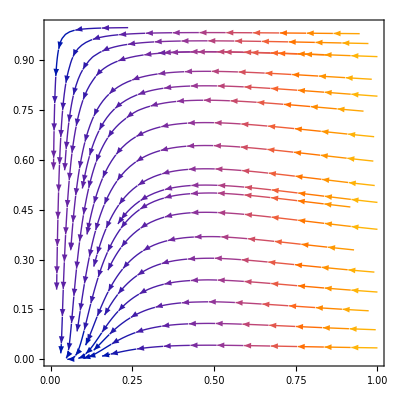

-Graphics-

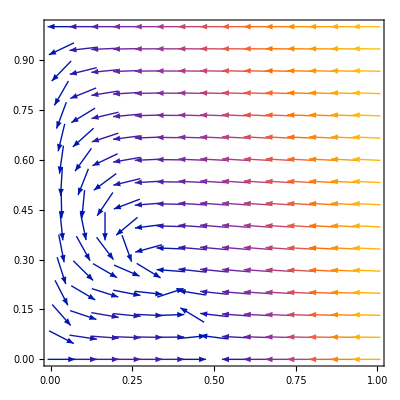

-Graphics-